```mathematica
Integrate[1,{x,-a,a}]
```

2 a

```mathematica
Integrate[1,
{x,-a,a},
{y,-b Sqrt[1-(x/a)^2],b Sqrt[1-(x/a)^2]},
Assumptions->a>0]
```

a b π

```mathematica
Integrate[1,
{x,-a,a},
{y,-b Sqrt[1-(x/a)^2],b Sqrt[1-(x/a)^2]},
{z,-c Sqrt[1-(x/a)^2-(y/b)^2],c Sqrt[1-(x/a)^2-(y/b)^2]},
Assumptions->a>0&&b∈Reals]
```

4/3 a b c π

```mathematica
Integrate[1,
{x,-a,a},
{y,-b Sqrt[1-(x/a)^2],b Sqrt[1-(x/a)^2]},
{z,-c Sqrt[1-(x/a)^2-(y/b)^2],c Sqrt[1-(x/a)^2-(y/b)^2]},
{w,-d Sqrt[1-(x/a)^2-(y/b)^2-(z/c)^2],d Sqrt[1-(x/a)^2-(y/b)^2-(z/c)^2]},
Assumptions->a>0&&b∈Reals&&c∈Reals]
```

1/2 a b c d π^2

```mathematica
V[n_,cs_]:=π^(n/2)/Gamma[(n/2)+1]*Times@@cs
```

```mathematica
V[2,{1,1}]
```

π

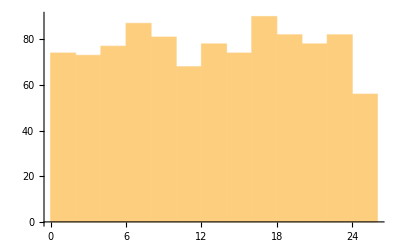

```mathematica
Histogram[Table[V[10,RandomReal[10]],{1000}]]
```

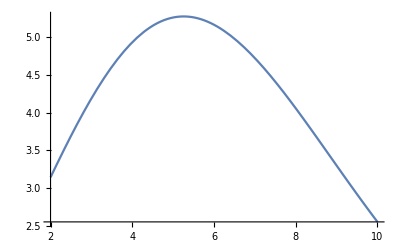

```mathematica
Plot[V[n,Table[1,{n}]],{n,2,10}]
```